# PLANO DE FOGO PARA BANCADAS Furos de Grande Diâmetro

Cálculo do Plano de Fogo para o desmonte de bancadas em minas a céu aberto segundo a metodologia de Jimeno, Jimeno e Carcedo em "Drilling and Blasting of Rocks" para furos de grande diâmetro (entre 180 mm e 450 mm).


-Graphics-

Dados de Entrada

```mathematica
TProdTon=2000000; (* Produção Total anual, t/ano *)
DensRocha=2.7;(* Densidade da rocha, t/m.b3 *)
TProd=TProdTon/DensRocha;(* Produção em m.b3/ano *)
Frequencia=1; (* Frequencia de detonação, fogo/semana *)
Turno=8;(* Preciso de ajuda, não sei o que é *)
VolFogo=(TProd Frequencia)/52;(* Volume desmontado por fogo, onde 52 é o número de semanas em 1 ano *)
EU=10;(* Espaço útil para trânsito de equipamentos, m *)
LarguraMax=100;(* Largura máxima da bancada *)
nMaxLinhas=5;(* Número Máximo de Linhas *)
ECol=1;(* Tipo do Explosivo da coluna, ANFO=1, EMulsão=2 *)
ρ1=0.8;(* Densidade do ANFO, g/cm^3 *)
ρ2=1.3; (* Densidade da Emulsão, g/cm^3 *)
RCU=150;(* Resistência à Compressão Uniaxial da Rocha, MPa *)
TamFig=480;(* Tamanho das Figuras *)
Calcular;
```

Parâmetros de Projeto

```mathematica
p={{52,40,28,33,38,45},{44,32,23,27,32,37},{37,25,21,24,30,34}};
i=Which[RCU<70,1,RCU<180,2,RCU≥180,3];
PMH=VolFogo/(Turno*7);(*Produção Média por Hora, m^3 b/h *)
d=Which[RCU<70&&PMH<600,0.2,RCU≤180&&PMH<150,0.2,RCU>180 &&PMH<50,0.2,RCU<70&&PMH<1200,0.25,RCU≤180&&PMH<300,0.25,RCU>180 &&PMH<125,0.25,RCU<70&&PMH≥2050,0.311,RCU≤180&&PMH≥625,0.311,RCU>180 &&PMH≥270,0.311];(* Diâmetro do Furo, mm *)
β=If[RCU<70&&H>24,10,0];
(* Inclinação do furo *)
```

Null^3

Cálculo do Plano de Fogo

```mathematica
H=p⟦i,1⟧d;(* Altura da Bancada, m *)
T=p⟦i,2⟧d ;(* Comprimento do Tampão, m *)
B=Which[ECol==1,p⟦i,3⟧d,ECol==2,p⟦i,5⟧d];(* Afastamento,
 m *)
S=Which[ECol==1,p⟦i,4⟧d,ECol==2,p⟦i,6⟧d];(* Espaçamento,
 m *)
J=8d;(* Comprimento da Subfuração,
m *)
```

Null^3

```mathematica
lf=8d; (* Comprimento da Carga de Fundo, m *)
L=H/Cos[β π/180]+(1-β/100)J;(* Comprimento do furo,
 m *)
VR=B S H/Cos[β π/180]; (* Volume de Rocha Desmontada, m^3 *)
RA=VR/L;(* Rendimento: Volume de Rocha Desmontada
 por m de Furo, m.b3/m *)

qf=((1000 π d^2) ρ2)/4 ;(* Concentração da Carga de
 Fundo, kg/m *)
Qf=lf qf;(* Carga do Fundo, kg *)
lc=L-T-lf;(* Comprimento da Carga de Coluna, m *)
qc=((1000 π d^2) ρ1)/4 ;(* Concentração da Carga de
 Coluna, kg/m *)
Qc=lc qc;(* Carga da Coluna, kg *)
Qb=Qf+Qc;(* Carga Total, kg *)
CE=Qb/VR;(* Consumo Específico de Explosivo,
kg/m^3 *)
```

Null^2

Null^3

Null^3

```mathematica
Tf=Ceiling[VolFogo/VR];(* Número de furos totais para atingir produção *)
For[n=1,n≤nMaxLinhas,n++,(* Laço para verificar o número adequado de linhas, iniciando em 1 *)
While[Mod[Tf,n]≠0,(* Enquanto a divisão entre total de furos e número não é inteira *)
Tf+=1(* Incrementa 1 até a divisão ser inteira *)
];
If[Tf*S/n+S<LarguraMax,(* Se a Largura da Bancada é menor que Largura Máxima*)
fpl=Tf/n;(* Número de furos por linha *)
Break[](* Termina o laço inteiro, pois é o valor otimizado *)
];
];
If[n≤nMaxLinhas&&S+fpl*S<LarguraMax,
LB=S+fpl*S;(* Largura da bancada adequada *)
PB=B+n*B+EU; (* Profundidade da bancada adequada *)
,
n=0;
fpl=0;
Print["Não será possível realizar o desmonte"]
];
```

Plano 2D

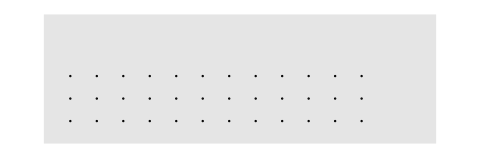

```mathematica
p1=Graphics[{Opacity[.1],Polygon[{{0,0},{LarguraMax,0},{LarguraMax,PB},{0,PB}}]}];
furos=Graphics[Table[Circle[{x,y},d/2],{x,S,LB-S,S},{y,B,n B,B}]];
g1=Show[{furos,p1},ImageSize->TamFig]
```

Plano 3D

```mathematica
p1=Graphics3D[{Opacity[.2],
Polygon[{{0,0,0},{LarguraMax,0,0},{LarguraMax,PB,0},{0,PB,0}}]}];
p2=Graphics3D[{Opacity[.2],
Polygon[{{0,0,0},{LarguraMax,0,0},{LarguraMax,-H Tan[β π/180],-H},{0,-H Tan[β π/180],-H}}]}];
p3=Graphics3D[{Opacity[.2],
Polygon[{{0,-H Tan[β π/180],-H},{LarguraMax,-H Tan[β π/180],-H},{LarguraMax,-H Tan[β π/180]-PB/2,-H},{0,-H Tan[β π/180]-PB/2,-H}}]}];
Tampao=Graphics3D[{Red,
Table[Cylinder[{{x,y,0},{x,y-(T) Sin[β π/180],-(T) Cos[β π/180]}},d/2],{x,S,LB-S,S},{y,B,n B,B}]}];
CargaColuna=Graphics3D[{Blue,
Table[Cylinder[{{x,y-(T) Sin[β π/180],-(T) Cos[β π/180]},{x,y-(T+lc) Sin[β π/180],-(T+lc) Cos[β π/180]}},d/2],{x,S,LB-S,S},{y,B,n B,B}]}];
CargaFundo=Graphics3D[{Purple,
Table[Cylinder[{{x,y-(T+lc) Sin[β π/180],-(T+lc) Cos[β π/180]},{x,y-(T+lc+lf) Sin[β π/180],-(T+lc+lf) Cos[β π/180]}},d/2],{x,S,LB-S,S},{y,B,n B,B}]}];
g2=Show[{p1,p2,p3,Tampao,CargaColuna,CargaFundo},Boxed->False,Axes->True,LabelStyle->(FontSize->20),ImageSize->TamFig]
g3=Show[{p1,p2,p3,Tampao,CargaColuna,CargaFundo},ViewPoint->{Infinity,0,0},Boxed->False,Axes->True,LabelStyle->(FontSize->20),ImageSize->TamFig]
Animate[With[{v=RotationTransform[θ,{0,0,1}][{1,10,1}]},Show[{p1,p2,p3,Tampao,CargaColuna,CargaFundo},Boxed->False,Axes-> False,ViewPoint->v,ImageSize->TamFig]],{θ,(3 π)/2,(7 π)/2},AnimationRate->0.05,AnimationRunning->False]
```

-Graphics3D-

-Graphics3D-

```mathematica
If[n≠0,
Print["\n- VARIÁVEIS DE PRODUÇÃO -"]Print["Produção desejada anual: ",TProdTon," ton - ",TProd," m^3"]Print["Densidade da rocha: ",DensRocha," t/m.b3"]Print["Frequência de execução: ",Frequencia," fogo/semana"]
Print["Produção média por hora: ",PMH," m^3/h"]
Print["Resistência à compressão uniaxial da rocha: ",RCU," MPa"]
Print["Inclinação do furo: ",β,"°"]
Print["Espaço útil da berma para trânsito de equipamentos: ",EU," m"]
Print["Densidade da carga do explosivo na coluna: ",ρ1," g/cm^3"]
Print["Densidade da carga do explosivo no fundo: ",ρ2," g/cm^3"]
Print["\n\n- PARÂMETROS DE PROJETO -"]
Print["Largura máxima disponível para execução: ",LarguraMax," m"]
Print["Largura da bancada do projeto: ",LB," m"]
Print["Comprimento da bancada do projeto: ", PB," m"]
Print["Altura da bancada: ",H," m"]
Print["Diâmetro do furo: ",d," m"]
Print["Afastamento: ",B, " m"]
Print["Espaçamento: ",S," m"]
Print["Comprimento total do furo: ",L," m"]
Print["Comprimento do tampão: ",T," m"]
Print["Comprimento da carga de coluna: ",lc," m"]
Print["Comprimento da carga de fundo: ",lf," m"]
Print["Comprimento da subfuração: ",J," m"]
Print["Volume de Rocha Desmontada por furo: ",VR," m^3"]
Print["Rendimento do Desmonte: ",RA," m^3/m"]
Print["Concentração da Carga de Fundo: ",qf," kg/m"]
Print["Carga de Fundo: ",Qf, " kg"]
Print["Concentração da Carga de Coluna: ",qc, " kg/m"]
Print["Carga de Coluna: ",Qc, " kg"]
Print["Carga total no furo: ",Qb,"kg"]
Print["Carga total de explosivo: ",Qb*Tf,"kg"]
Print["Consumo específico de explosivo: ",CE," kg/m^3"]
];
```

```mathematica
Nome="Mina de granito";
Export[NotebookDirectory[]<>Nome<>" - Vista de Topo.gif",g1,"GIF"];
Export[NotebookDirectory[]<>Nome<>" - Vista 3D.gif",g2,"GIF"];
Export[NotebookDirectory[]<>Nome<>" - Vista Lateral.gif",g3,"GIF"];

Saida=OpenWrite[NotebookDirectory[]<>Nome<>" - Resultados.txt",CharacterEncoding->"Unicode"];
WriteString[Saida,"RESULTADOS DA SIMULAÇÃO: '",Nome,"' \n"];
WriteString[Saida,"\n\n- VARIÁVEIS DE PRODUÇÃO -\n\n"]
WriteString[Saida,"Produção desejada anual: ",TProdTon," ton - ",TProd," m.b3\n"]
WriteString[Saida,"Densidade da rocha: ",DensRocha," t/m.b3\n"]
WriteString[Saida,"Frequência de desmonte: ", Frequencia," fogo/semana\n"]
WriteString[Saida, "Volume desmontado necessário por fogo: ",VolFogo," m.b3\n"]
WriteString[Saida,"Produção média por hora: ",PMH," m.b3/h\n"]
WriteString[Saida,"Resistência à compressão uniaxial da rocha: ",RCU," MPa\n"]
WriteString[Saida,"Inclinação do furo: ",β,"°\n"]
WriteString[Saida,"Espaço útil da berma para trânsito de equipamentos: ",EU," m\n"]
WriteString[Saida,"Densidade da carga do explosivo na coluna: ",ρ1," g/cm.b3\n"]
WriteString[Saida,"Densidade da carga do explosivo no fundo: ",ρ2," g/cm.b3\n"]
WriteString[Saida,"\n- PARÂMETROS DE PROJETO -\n\n"]
WriteString[Saida,"Largura máxima disponível para execução: ", LarguraMax," m\n"]
WriteString[Saida,"Largura da bancada: ",LB," m\n"]
WriteString[Saida,"Profundidade da bancada: ", PB," m\n"]
WriteString[Saida,"Altura da bancada: ",H," m\n"]
WriteString[Saida,"Número total de linhas: ",n"linhas x ",fpl," = ",n*fpl," furos\n"]
WriteString[Saida,"Diâmetro dos furos: ",d," m\n"]
WriteString[Saida,"Afastamento: ",B, " m\n"]
WriteString[Saida,"Espaçamento: ",S," m\n"]
WriteString[Saida,"Comprimento total do furo: ",L," m\n"]
WriteString[Saida,"Comprimento do tampão: ",T," m\n"]
WriteString[Saida,"Comprimento da carga de coluna: ",lc," m\n"]
WriteString[Saida,"Comprimento da carga de fundo: ",lf," m\n"]
WriteString[Saida,"Comprimento da subfuração: ",J," m\n"]
WriteString[Saida,"Volume de Rocha Desmontada por furo: ",VR," m.b3\n"]
WriteString[Saida,"Volume Total de Rocha Desmontada: ",VR*Tf," m.b3\n"]
WriteString[Saida,"Rendimento do Desmonte: ",RA," m.b3/m\n"]
WriteString[Saida,"Concentração da Carga de Fundo: ",qf," kg/m\n"]
WriteString[Saida,"Carga de Fundo: ",Qf, " kg\n"]
WriteString[Saida,"Concentração da Carga de Coluna: ",qc, " kg/m\n"]
WriteString[Saida,"Carga de Coluna: ",Qc, " kg\n"]
WriteString[Saida,"Carga total no furo: ",Qb,"kg\n"]
WriteString[Saida,"Carga total de explosivo: ",Qb*Tf,"kg\n"]
WriteString[Saida,"Consumo específico: ",CE," kg/m.b3\n"]
Close[Saida];
```